What We Haven’t Discussed

There’s a lot more to the Wolfram Language than we’ve been able to cover in this book. Here’s a sampling of just a few of the many topics and areas that we’ve missed.

#### User Interface Construction

Set up a tabbed interface:

```mathematica
TabView[Table[ListPlot[Range[20]^n],{n,5}]]
```

12345

User interfaces are just another type of symbolic expression; make a grid of sliders:

```mathematica
Grid[Table[Slider[ ],4,3]]
```

|  | 
 |  | 
 |  | 
 |  |

#### Function Visualization

Plot a function:

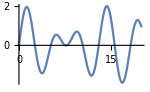

```mathematica
Plot[Sin[x]+Sin[Sqrt[2] x],{x,0,20}]
```

3D contour plot:

```mathematica
ContourPlot3D[x^3+y^2-z^2,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

#### Mathematical Computation

Do symbolic computations, with x as an algebraic variable:

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

Get symbolic solutions to equations:

```mathematica
Solve[x^3-2x+1==0,x]
```

{{x→1},{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

Do calculus symbolically:

```mathematica
Integrate[Sqrt[x+Sqrt[x]],x]
```

1/12 √(√x+x) (-3+2 √x+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

Display results in traditional mathematical form:

```mathematica
Integrate[AiryAi[x],x]//TraditionalForm
```

-(x (3^(1/3) x (2/3)^2 _1 F_2(2/3;4/3,5/3;x^3/9)-3 1/3 5/3 _1 F_2(1/3;2/3,4/3;x^3/9)))/(9 3^(2/3) 2/3 4/3 5/3)

Use 2D notation for input:

```mathematica
∑_(i=0)^n (Binomial[n,i] i!)/((n+1+i)!)
```

(√π)/(2 (1/2 (1+2 n))!)

#### Numerics

Minimize a function inside a spherical ball:

```mathematica
NMinimize[{x^4+y^4-z/(x+1),y>0},{x,y,z}∈Ball[ ]]
```

{-7.34516,{x→-0.971029,y→0.0139884,z→0.238555}}

Solve a differential equation to get an approximate function:

```mathematica
NDSolve[{y''[x]+ Sin[y[x]]y[x]==0,y[0]==1,y'[0]==0},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

Make a plot using the approximate function:

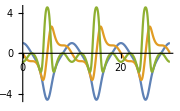

```mathematica
Plot[Evaluate[{y[x],y'[x],y''[x]}/.%],{x,0,30}]
```

#### Geometry

The area of a disk (filled circle) of radius r:

```mathematica
Area[Disk[{0,0},r]]
```

π r^2

Make a shape by “shrinkwrapping” around 100 random points in 3D:

```mathematica
ConvexHullMesh[RandomReal[1,{100,3}]]
```

-Graphics-

#### Algorithms

Find the shortest tour of the capitals of Europe (traveling salesman problem):

```mathematica
With[{c=LinguisticAssistant},GeoListPlot[c[[Last@FindShortestTour[c]]],Joined->True]]
```

-Graphics-

Factor a big number:

```mathematica
FactorInteger[2^255-1]
```

{{7,1},{31,1},{103,1},{151,1},{2143,1},{11119,1},{106591,1},{131071,1},{949111,1},{9520972806333758431,1},{5702451577639775545838643151,1}}

#### Logic

Make a truth table:

```mathematica
BooleanTable[p||q&&(p||!q),{p},{q}]//Grid
```

True | True
False | False

Find a minimal representation of a Boolean function:

```mathematica
BooleanMinimize[BooleanCountingFunction[{2,3},{a,b,c,d}]]//TraditionalForm
```

(a∧b∧¬d)∨(a∧¬b∧c)∨(a∧¬c∧d)∨(¬a∧b∧d)∨(b∧c∧¬d)∨(¬b∧c∧d)

#### The Computational Universe

Run my favorite example of a very simple program with very complex behavior:

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},200]]
```

-Graphics-

RulePlot shows the underlying rule:

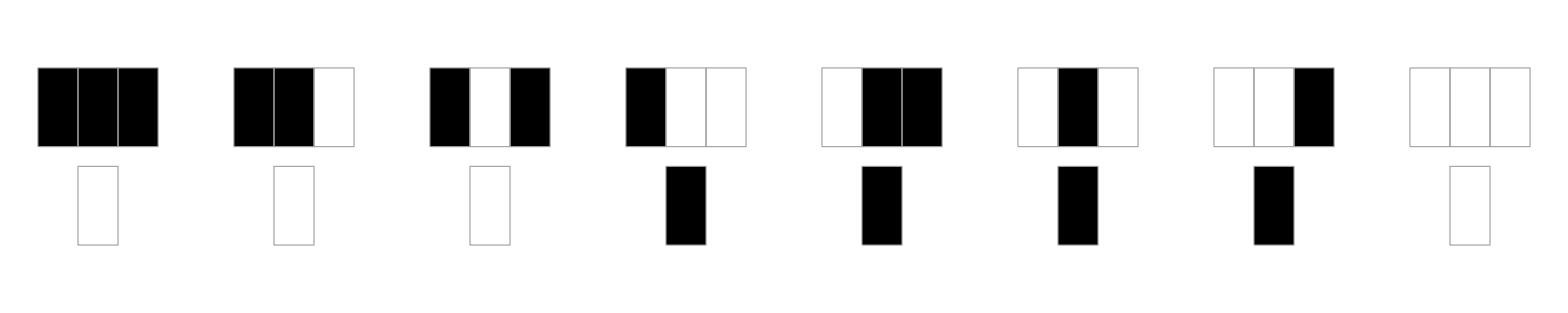

```mathematica
RulePlot[CellularAutomaton[30]]
```

#### Building APIs

Deploy a simple web API that finds the distance from a specified location:

```mathematica
CloudDeploy[APIFunction[{"loc" -> "Location"}, GeoDistance[#loc, Here] &]]
```

CloudObject[]

Create embeddable code for an external Java program to call the API:

```mathematica
EmbedCode[%,"Java"]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from Java:
Code
 | Copy to Clipboard
import java.net.URL;
import java.net.HttpURLConnection;
import java.net.URLEncoder;
import java.io.InputStream;
import java.io.BufferedReader;
import java.io.InputStreamReader;
import java.io.DataOutputStream;
import java.io.IOException;

public class WolframCloudCall {

    public static String call(String loc) throws IOException {

        URL _url = new URL("http://www.wolframcloud.com/objects/09302cdc-4d52-457e-86ae-b834bd9717ae");
        HttpURLConnection _conn = (HttpURLConnection) _url.openConnection();
        _conn.setRequestMethod("POST");
        _conn.setDoOutput(true);
        _conn.setDoInput(true);
        _conn.setUseCaches(false);
        _conn.setAllowUserInteraction(false);
        _conn.setRequestProperty("Content-Type", "application/x-www-form-urlencoded; charset=utf-8");
        _conn.setRequestProperty("User-Agent", "EmbedCode-Java/1.0");
        DataOutputStream _out = new DataOutputStream(_conn.getOutputStream());

        _out.writeBytes("loc");
        _out.writeBytes("=");
        _out.writeBytes(URLEncoder.encode("" + loc, "UTF-8"));
        _out.writeBytes("&");

        _out.close();

        if (_conn.getResponseCode() != 200) {
            throw new IOException(_conn.getResponseMessage());
        }
        
        BufferedReader _rdr = new BufferedReader(new InputStreamReader(_conn.getInputStream()));
        StringBuilder _sb = new StringBuilder();
        String _line;
        while ((_line = _rdr.readLine()) != null) {
            _sb.append(_line);
        }
        _rdr.close();
        _conn.disconnect();
        return _sb.toString();
    }
}

#### Document Generation

Documents are symbolic expressions, like everything else:

```mathematica
DocumentNotebook[{Style["A Circle","Section"],Style["How to make a circle"],Graphics[Circle[ ]]}]
```

A Circle
How to make a circle
-Graphics-

#### Evaluation Control

Hold a computation unevaluated:

```mathematica
Hold[2+2==4]
```

Hold[2+2==4]

Release the hold:

```mathematica
ReleaseHold[%]
```

True

#### Systems-Level Operations

Run an external process (not allowed in the cloud!):

```mathematica
RunProcess["ps","StandardOutput"]
```

PID TTY           TIME CMD
  374 ttys000    0:00.03 -tcsh
40192 ttys000    0:00.66 ssh pi
60521 ttys001    0:00.03 -tcsh

Encrypt anything:

```mathematica
Encrypt["sEcreTkey","Read this if you can!"]
```

EncryptedObject[<|Data -> ByteArray[<32>], InitializationVector -> ByteArray[<16>], OriginalForm -> String|>]

#### Parallel Computation

I’m running on a 12-core machine:

```mathematica
$ProcessorCount
```

12

Sequentially test a sequence of (big) numbers for primality, and find the total time taken:

```mathematica
Table[PrimeQ[2^Prime[n]-1],{n,500}]//Counts//AbsoluteTiming
```

{4.15402,<|True→18,False→482|>}

Doing the same thing in parallel takes considerably less time:

```mathematica
ParallelTable[PrimeQ[2^Prime[n]-1],{n,500}]//Counts//AbsoluteTiming
```

{0.572106,<|True→18,False→482|>}